```mathematica
m[s_,l1_,l2_,l3_,l4_,l5_,l6_,l7_,l8_,l9_,l10_,l11_,b9a_,b9b_]:= {{s+l1,0,0,0,0,0,0,0,0,0,0,0},{-l1,s+l2,0,0,0,0,0,0,0,0,0,0},{0,-l2,s+l3,0,0,0,0,0,0,0,0,0},{0,0,-l3,s+l4,0,0,0,0,0,0,0,0},{0,0,0,-l4, s+l5, 0,0,0,0,0,0,0}, {0,0,0,0, -l5, s+l6,0,0,0,0,0,0},{0,0,0,0,0,-l6, s+ l7,0,0,0,0,0},{0, 0, 0, 0, 0, 0, -l7, s+l8,0,0,0,0},{0,0,0,0,0,0,0,-l8, s+l9, 0, 0, 0}, {0,0,0,0,0,0,0,0,-l9*b9b, s+l10,0,0},{0,0,0,0,0,0,0,0,-l9*b9a,0,s+l11,0},{0,0,0,0,0,0,0,0,0,-l10,-l11,s}}
```

```mathematica
MatrixForm[{{s+l1,0,0,0,0,0,0,0,0,0,0,0},{-l1,s+l2,0,0,0,0,0,0,0,0,0,0},{0,-l2,s+l3,0,0,0,0,0,0,0,0,0},{0,0,-l3,s+l4,0,0,0,0,0,0,0,0},{0,0,0,-l4, s+l5, 0,0,0,0,0,0,0}, {0,0,0,0, -l5, s+l6,0,0,0,0,0,0},{0,0,0,0,0,-l6, s+ l7,0,0,0,0,0},{0, 0, 0, 0, 0, 0, -l7, s+l8,0,0,0,0},{0,0,0,0,0,0,0,-l8, s+l9, 0, 0, 0}, {0,0,0,0,0,0,0,0,-l9*b9b, s+l10,0,0},{0,0,0,0,0,0,0,0,-l9*b9a,0,s+l11,0},{0,0,0,0,0,0,0,0,0,-l10,-l11,s}}]
```

(l1+s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-l1 | l2+s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -l2 | l3+s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -l3 | l4+s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -l4 | l5+s | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -l5 | l6+s | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -l6 | l7+s | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -l7 | l8+s | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -l8 | l9+s | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -b9b l9 | l10+s | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -b9a l9 | 0 | l11+s | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -l10 | -l11 | s)

```mathematica
invm[s_,l1_,l2_,l3_,l4_,l5_,l6_,l7_,l8_,l9_,l10_,l11_,b9a_,b9b_]:= Inverse[m[s,l1,l2,l3,l4,l5,l6,l7,l8,l9,l10,l11,b9a,b9b]]
```

```mathematica
invm[s,l1,l2,l3,l4,l5,l6,l7,l8,l9,l10,l11,b9a,b9b]
```

{{1/(l1+s),0,0,0,0,0,0,0,0,0,0,0},{l1/((l1+s) (l2+s)),1/(l2+s),0,0,0,0,0,0,0,0,0,0},{(l1 l2)/((l1+s) (l2+s) (l3+s)),l2/((l2+s) (l3+s)),1/(l3+s),0,0,0,0,0,0,0,0,0},{(l1 l2 l3)/((l1+s) (l2+s) (l3+s) (l4+s)),(l2 l3)/((l2+s) (l3+s) (l4+s)),l3/((l3+s) (l4+s)),1/(l4+s),0,0,0,0,0,0,0,0},{(l1 l2 l3 l4)/((l1+s) (l2+s) (l3+s) (l4+s) (l5+s)),(l2 l3 l4)/((l2+s) (l3+s) (l4+s) (l5+s)),(l3 l4)/((l3+s) (l4+s) (l5+s)),l4/((l4+s) (l5+s)),1/(l5+s),0,0,0,0,0,0,0},{(l1 l2 l3 l4 l5)/((l1+s) (l2+s) (l3+s) (l4+s) (l5+s) (l6+s)),(l2 l3 l4 l5)/((l2+s) (l3+s) (l4+s) (l5+s) (l6+s)),(l3 l4 l5)/((l3+s) (l4+s) (l5+s) (l6+s)),(l4 l5)/((l4+s) (l5+s) (l6+s)),l5/((l5+s) (l6+s)),1/(l6+s),0,0,0,0,0,0},{(l1 l2 l3 l4 l5 l6)/((l1+s) (l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s)),(l2 l3 l4 l5 l6)/((l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s)),(l3 l4 l5 l6)/((l3+s) (l4+s) (l5+s) (l6+s) (l7+s)),(l4 l5 l6)/((l4+s) (l5+s) (l6+s) (l7+s)),(l5 l6)/((l5+s) (l6+s) (l7+s)),l6/((l6+s) (l7+s)),1/(l7+s),0,0,0,0,0},{(l1 l2 l3 l4 l5 l6 l7)/((l1+s) (l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s)),(l2 l3 l4 l5 l6 l7)/((l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s)),(l3 l4 l5 l6 l7)/((l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s)),(l4 l5 l6 l7)/((l4+s) (l5+s) (l6+s) (l7+s) (l8+s)),(l5 l6 l7)/((l5+s) (l6+s) (l7+s) (l8+s)),(l6 l7)/((l6+s) (l7+s) (l8+s)),l7/((l7+s) (l8+s)),1/(l8+s),0,0,0,0},{(l1 l2 l3 l4 l5 l6 l7 l8)/((l1+s) (l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(l2 l3 l4 l5 l6 l7 l8)/((l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(l3 l4 l5 l6 l7 l8)/((l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(l4 l5 l6 l7 l8)/((l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(l5 l6 l7 l8)/((l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(l6 l7 l8)/((l6+s) (l7+s) (l8+s) (l9+s)),(l7 l8)/((l7+s) (l8+s) (l9+s)),l8/((l8+s) (l9+s)),1/(l9+s),0,0,0},{(b9b l1 l2 l3 l4 l5 l6 l7 l8 l9)/((l1+s) (l10+s) (l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(b9b l2 l3 l4 l5 l6 l7 l8 l9)/((l10+s) (l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(b9b l3 l4 l5 l6 l7 l8 l9)/((l10+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(b9b l4 l5 l6 l7 l8 l9)/((l10+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(b9b l5 l6 l7 l8 l9)/((l10+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(b9b l6 l7 l8 l9)/((l10+s) (l6+s) (l7+s) (l8+s) (l9+s)),(b9b l7 l8 l9)/((l10+s) (l7+s) (l8+s) (l9+s)),(b9b l8 l9)/((l10+s) (l8+s) (l9+s)),(b9b l9)/((l10+s) (l9+s)),1/(l10+s),0,0},{(b9a l1 l2 l3 l4 l5 l6 l7 l8 l9)/((l1+s) (l11+s) (l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(b9a l2 l3 l4 l5 l6 l7 l8 l9)/((l11+s) (l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(b9a l3 l4 l5 l6 l7 l8 l9)/((l11+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(b9a l4 l5 l6 l7 l8 l9)/((l11+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(b9a l5 l6 l7 l8 l9)/((l11+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(b9a l6 l7 l8 l9)/((l11+s) (l6+s) (l7+s) (l8+s) (l9+s)),(b9a l7 l8 l9)/((l11+s) (l7+s) (l8+s) (l9+s)),(b9a l8 l9)/((l11+s) (l8+s) (l9+s)),(b9a l9)/((l11+s) (l9+s)),0,1/(l11+s),0},{(l1 l2 l3 l4 l5 l6 l7 l8 (b9a l10 l11 l9+b9b l10 l11 l9+b9b l10 l9 s+b9a l11 l9 s))/(s (l1+s) (l10+s) (l11+s) (l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(l2 l3 l4 l5 l6 l7 l8 (b9a l10 l11 l9+b9b l10 l11 l9+b9b l10 l9 s+b9a l11 l9 s))/(s (l10+s) (l11+s) (l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(l3 l4 l5 l6 l7 l8 (b9a l10 l11 l9+b9b l10 l11 l9+b9b l10 l9 s+b9a l11 l9 s))/(s (l10+s) (l11+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(l4 l5 l6 l7 l8 (b9a l10 l11 l9+b9b l10 l11 l9+b9b l10 l9 s+b9a l11 l9 s))/(s (l10+s) (l11+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(l5 l6 l7 l8 (b9a l10 l11 l9+b9b l10 l11 l9+b9b l10 l9 s+b9a l11 l9 s))/(s (l10+s) (l11+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),(l6 l7 l8 (b9a l10 l11 l9+b9b l10 l11 l9+b9b l10 l9 s+b9a l11 l9 s))/(s (l10+s) (l11+s) (l6+s) (l7+s) (l8+s) (l9+s)),(l7 l8 (b9a l10 l11 l9+b9b l10 l11 l9+b9b l10 l9 s+b9a l11 l9 s))/(s (l10+s) (l11+s) (l7+s) (l8+s) (l9+s)),(l8 (b9a l10 l11 l9+b9b l10 l11 l9+b9b l10 l9 s+b9a l11 l9 s))/(s (l10+s) (l11+s) (l8+s) (l9+s)),(b9a l10 l11 l9+b9b l10 l11 l9+b9b l10 l9 s+b9a l11 l9 s)/(s (l10+s) (l11+s) (l9+s)),l10/(s (l10+s)),(-b9b l10 l9 (l1+s) (l11+s) (l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)-(l1+s) (l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s) (-b9a l11 l9 (l10+s)-b9b l10 l9 (l11+s)))/(b9a l9 s (l1+s) (l10+s) (l11+s) (l2+s) (l3+s) (l4+s) (l5+s) (l6+s) (l7+s) (l8+s) (l9+s)),1/s}}

```mathematica
Subscript[N, 0] = {1,0,0,0,0,0,0,0,0,0,0,0}
```

{1,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
R0[s_,l1_,l2_,l3_,l4_,l5_,l6_,l7_,l8_,l9_,l10_,l11_,b9a_,b9b_]:=invm[s,l1,l2,l3,l4,l5, l6, l7, l8, l9, l10, l11, b9a, b9b].Subscript[N, 0]
```

```mathematica
N1s[s_,l1_]:=Simplify[R0[s,l1,0,0,0,0,0,0,0,0,0,0,0,0][[1]]]
```

```mathematica
N1[t_,l1_] :=Simplify[InverseLaplaceTransform[N1s[s,l1],s,t]]
```

```mathematica
N1[0.5,1.0]
```

0.606531

```mathematica
N2s[s_,l1_, l2_]:=Simplify[R0[s,l1,l2,0,0,0,0,0,0,0,0,0,0,0][[2]]]
```

```mathematica
N2[t_,l1_,l2_] :=Simplify[InverseLaplaceTransform[N2s[s,l1,l2],s,t]]
```

```mathematica
N2[t,l1,l2]
```

-((ⅇ^(-l1 t)-ⅇ^(-l2 t)) l1)/(l1-l2)

```mathematica
N3s[s_,l1_, l2_, l3_]:=Simplify[R0[s,l1,l2,l3,0,0,0,0,0,0,0,0,0,0][[3]]]
```

```mathematica
N3[t_,l1_,l2_, l3_] :=Simplify[InverseLaplaceTransform[N3s[s,l1,l2, l3],s,t]]
```

```mathematica
N3[t,l1,l2,l3]
```

(ⅇ^(-((l1+l2+l3) t)) l1 l2 (ⅇ^((l1+l2) t) (l1-l2)+ⅇ^((l2+l3) t) (l2-l3)+ⅇ^((l1+l3) t) (-l1+l3)))/((l1-l2) (l1-l3) (l2-l3))

```mathematica
Subscript[f, 2][t_,l1_,l2_]:=N2[t,l1,l2]/N1[t,l1]
```

```mathematica
Subscript[f, 3][t_,l1_,l2_,l3_]:= N3[t,l1,l2,l3]/N1[t,l1]
```

```mathematica
p2[l1_,l2_,l3_] := LogPlot[Subscript[f, 2][t,l1,l2],{t,0.,100.},PlotRange->Automatic,PlotStyle->Blue];
```

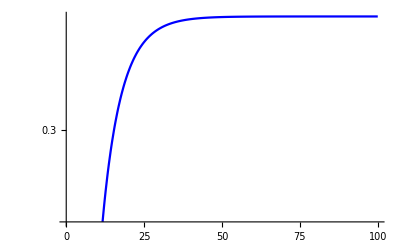

```mathematica
p2[0.05,1/5,0]
```

```mathematica
p3[l1_,l2_,l3_] := LogPlot[Subscript[f, 3][t,l1,l2,l3],{t,0.,100.},PlotRange->Automatic,PlotStyle->Orange];
```

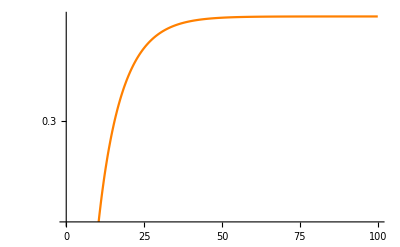

```mathematica
p3[0.05,1/5,1/5]
```

```mathematica
Manipulate[Show[p2[l1,l2,l3],p3[l1,l2,l3],PlotRange->Automatic],{l1,1/10000,1/100},{l2,1/5,1/2},{l3,1/5,1/2}]
```

```mathematica
N4s[s_,l1_, l2_, l3_, l4_]:=Simplify[R0[s,l1,l2,l3,l4,0,0,0,0,0,0,0,0,0][[4]]]
```

```mathematica
N4[t_,l1_,l2_, l3_, l4_] :=Simplify[InverseLaplaceTransform[N4s[s,l1,l2, l3,l4],s,t]]
N4[t,l1,l2,l3,l4]
```

l1 l2 l3 (-ⅇ^(-l1 t)/((l1-l2) (l1-l3) (l1-l4))+ⅇ^(-l2 t)/((l1-l2) (l2-l3) (l2-l4))+ⅇ^(-l3 t)/((l1-l3) (-l2+l3) (l3-l4))+ⅇ^(-l4 t)/((l1-l4) (-l2+l4) (-l3+l4)))

```mathematica
Subscript[f, 4][t_,l1_,l2_,l3_, l4_]:= N4[t,l1,l2,l3,l4]/N1[t,l1]
```

```mathematica
p4[l1_,l2_,l3_,l4_] := LogPlot[Subscript[f, 4][t,l1,l2,l3,l4],{t,0.,100.},PlotRange->Automatic,PlotStyle->Magenta,PlotLabels->{"f4"}];
```

```mathematica
p4[0.05,1/5,1/5,1/5]
```

-Graphics-

```mathematica
Manipulate[Show[p2[l1,l2,l3],p3[l1,l2,l3],p4[l1,l2,l3,l4],PlotRange->Automatic,PlotLabels->Placed[{"f2","f3","f4"},Above]],{l1,1/10000,1/100},{l2,1/5,1/2},{l3,1/5,1/2},{l4,1/5,1/2}]
```

```mathematica
Manipulate[Show[p2[l1,l2,l3],p3[l1,l2,l3],p4[l1,l2,l3,l4],PlotRange->Automatic,PlotLabels->Placed[{"f2","f3","f4"},Above]],{l1,1/10000,1/100},{l2,1/5,1/2},{l3,1/5,1/2},{l4,1/5,1/2}]
```

```mathematica
Subscript[f, 2][t,l1,l2]
```

-(ⅇ^(l1 t) (ⅇ^(-l1 t)-ⅇ^(-l2 t)) l1)/(l1-l2)

```mathematica
Subscript[f, 2,a][t_,l1_,l2_] := (l1/l2)*(1/(1-(l1/l2)))
```

```mathematica
p2a[l1_,l2_,l3_] := LogPlot[Subscript[f, 2,a][t,l1,l2],{t,0.,100.},PlotRange->Automatic,PlotStyle->{Blue,Dashed}];
```

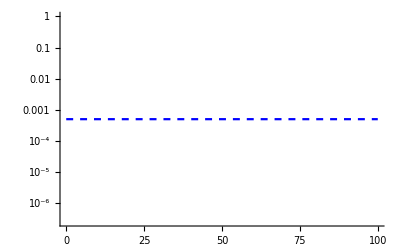

```mathematica
p2a[1/10000,1/5,0]
```

```mathematica
Manipulate[Show[p2[l1,l2,l3],p3[l1,l2,l3],p4[l1,l2,l3,l4],p2a[l1,l2,l3],PlotRange->Automatic,PlotLabels->Placed[{"f2","f3","f4"},Above]],{l1,1/10000,1/100},{l2,1/5,1/2},{l3,1/5,1/2},{l4,1/5,1/2}]
```

```mathematica
Series[Subscript[f, 2][t,l1,l2]/. l1-> z l2,{z,0,5}]/.z-> (Subscript[λ, 1]/Subscript[λ, 2]) //Quiet//TraditionalForm
```

(λ_1 (1-ⅇ^(-l2 t)))/λ_2+(λ_1/λ_2)^2 ⅇ^(-l2 t) (-l2 t+ⅇ^(l2 t)-1)+1/2 (λ_1/λ_2)^3 ⅇ^(-l2 t) (-l2^2 t^2-2 l2 t+2 ⅇ^(l2 t)-2)+1/6 (λ_1/λ_2)^4 ⅇ^(-l2 t) (-l2^3 t^3-3 l2^2 t^2-6 l2 t+6 ⅇ^(l2 t)-6)+1/24 (λ_1/λ_2)^5 ⅇ^(-l2 t) (-l2^4 t^4-4 l2^3 t^3-12 l2^2 t^2-24 l2 t+24 ⅇ^(l2 t)-24)+O((λ_1/λ_2)^6)

```mathematica
N5s[s_,l1_, l2_, l3_, l4_, l5_]:=Simplify[R0[s,l1,l2,l3,l4,l5,0,0,0,0,0,0,0,0][[5]]]
```

```mathematica
N5[t_,l1_,l2_, l3_, l4_, l5_] :=Simplify[InverseLaplaceTransform[N5s[s,l1,l2, l3,l4,l5],s,t]]
```

```mathematica
N5[t,l1,l2,l3,l4,l5]
```

l1 l2 l3 l4 (ⅇ^(-l1 t)/((l1-l2) (l1-l3) (l1-l4) (l1-l5))+ⅇ^(-l2 t)/((-l1+l2) (l2-l3) (l2-l4) (l2-l5))+ⅇ^(-l3 t)/((-l1+l3) (-l2+l3) (l3-l4) (l3-l5))+ⅇ^(-l4 t)/((-l1+l4) (-l2+l4) (-l3+l4) (l4-l5))+ⅇ^(-l5 t)/((-l1+l5) (-l2+l5) (-l3+l5) (-l4+l5)))

```mathematica
Subscript[f, 5][t_,l1_,l2_,l3_, l4_, l5_]:= N5[t,l1,l2,l3,l4,l5]/N1[t,l1]
```

```mathematica
Subscript[f, 5][t,l1,l2,l3, l4, l5]
```

ⅇ^(l1 t) l1 l2 l3 l4 (ⅇ^(-l1 t)/((l1-l2) (l1-l3) (l1-l4) (l1-l5))+ⅇ^(-l2 t)/((-l1+l2) (l2-l3) (l2-l4) (l2-l5))+ⅇ^(-l3 t)/((-l1+l3) (-l2+l3) (l3-l4) (l3-l5))+ⅇ^(-l4 t)/((-l1+l4) (-l2+l4) (-l3+l4) (l4-l5))+ⅇ^(-l5 t)/((-l1+l5) (-l2+l5) (-l3+l5) (-l4+l5)))

```mathematica
N6s[s_,l1_, l2_, l3_, l4_, l5_, l6_]:=Simplify[R0[s,l1,l2,l3,l4,l5,l6,0,0,0,0,0,0,0][[6]]]
```

```mathematica
N6[t_,l1_,l2_, l3_, l4_, l5_, l6_] :=Simplify[InverseLaplaceTransform[N6s[s,l1,l2, l3,l4,l5, l6],s,t]]
```

```mathematica
Subscript[f, 6][t_,l1_,l2_,l3_, l4_, l5_, l6_]:= N6[t,l1,l2,l3,l4,l5, l6]/N1[t,l1]
```

```mathematica
Subscript[f, 6][t,l1,l2,l3, l4, l5, l6]
```

ⅇ^(l1 t) l1 l2 l3 l4 l5 (-ⅇ^(-l1 t)/((l1-l2) (l1-l3) (l1-l4) (l1-l5) (l1-l6))+ⅇ^(-l2 t)/((l1-l2) (l2-l3) (l2-l4) (l2-l5) (l2-l6))+ⅇ^(-l3 t)/((l1-l3) (-l2+l3) (l3-l4) (l3-l5) (l3-l6))+ⅇ^(-l4 t)/((l1-l4) (-l2+l4) (-l3+l4) (l4-l5) (l4-l6))+ⅇ^(-l5 t)/((l1-l5) (-l2+l5) (-l3+l5) (-l4+l5) (l5-l6))+ⅇ^(-l6 t)/((l1-l6) (-l2+l6) (-l3+l6) (-l4+l6) (-l5+l6)))

```mathematica
N7s[s_,l1_, l2_, l3_, l4_, l5_, l6_, l7_]:=Simplify[R0[s,l1,l2,l3,l4,l5,l6,l7,0,0,0,0,0,0][[7]]]
```

```mathematica
N7[t_,l1_,l2_, l3_, l4_, l5_, l6_, l7_] :=Simplify[InverseLaplaceTransform[N7s[s,l1,l2, l3,l4,l5, l6, l7],s,t]]
```

```mathematica
Subscript[f, 7][t_,l1_,l2_,l3_, l4_, l5_, l6_, l7_]:= N7[t,l1,l2,l3,l4,l5, l6, l7]/N1[t,l1]
```

```mathematica
N8s[s_,l1_, l2_, l3_, l4_, l5_, l6_, l7_, l8_]:=Simplify[R0[s,l1,l2,l3,l4,l5,l6,l7,l8,0,0,0,0,0][[8]]]
```

```mathematica
N8[t_,l1_,l2_, l3_, l4_, l5_, l6_, l7_, l8_] :=Simplify[InverseLaplaceTransform[N8s[s,l1,l2, l3,l4,l5, l6, l7, l8],s,t]]
```

```mathematica
Subscript[f, 8][t_,l1_,l2_,l3_, l4_, l5_, l6_, l7_, l8_]:= N8[t,l1,l2,l3,l4,l5, l6, l7, l8]/N1[t,l1]
```

```mathematica
N9s[s_,l1_, l2_, l3_, l4_, l5_, l6_, l7_, l8_, l9_]:=Simplify[R0[s,l1,l2,l3,l4,l5,l6,l7,l8,l9,0,0,0,0][[9]]]
```

```mathematica
N9[t_,l1_,l2_, l3_, l4_, l5_, l6_, l7_, l8_, l9_] :=Simplify[InverseLaplaceTransform[N9s[s,l1,l2, l3,l4,l5, l6, l7, l8, l9],s,t]]
```

```mathematica
Subscript[f, 9][t_,l1_,l2_,l3_, l4_, l5_, l6_, l7_, l8_, l9_]:= N9[t,l1,l2,l3,l4,l5, l6, l7, l8, l9]/N1[t,l1]
```

```mathematica
Subscript[f, 7][t,l1, l2, l3, l4, l5, l6, l7]
```

ⅇ^(l1 t) l1 l2 l3 l4 l5 l6 (ⅇ^(-l1 t)/((l1-l2) (l1-l3) (l1-l4) (l1-l5) (l1-l6) (l1-l7))+ⅇ^(-l2 t)/((-l1+l2) (l2-l3) (l2-l4) (l2-l5) (l2-l6) (l2-l7))+ⅇ^(-l3 t)/((-l1+l3) (-l2+l3) (l3-l4) (l3-l5) (l3-l6) (l3-l7))+ⅇ^(-l4 t)/((-l1+l4) (-l2+l4) (-l3+l4) (l4-l5) (l4-l6) (l4-l7))+ⅇ^(-l5 t)/((-l1+l5) (-l2+l5) (-l3+l5) (-l4+l5) (l5-l6) (l5-l7))+ⅇ^(-l6 t)/((-l1+l6) (-l2+l6) (-l3+l6) (-l4+l6) (-l5+l6) (l6-l7))+ⅇ^(-l7 t)/((-l1+l7) (-l2+l7) (-l3+l7) (-l4+l7) (-l5+l7) (-l6+l7)))

```mathematica
Subscript[f, 8][t,l1, l2, l3, l4, l5, l6, l7, l8]
```

ⅇ^(l1 t) l1 l2 l3 l4 l5 l6 l7 (-ⅇ^(-l1 t)/((l1-l2) (l1-l3) (l1-l4) (l1-l5) (l1-l6) (l1-l7) (l1-l8))+ⅇ^(-l2 t)/((l1-l2) (l2-l3) (l2-l4) (l2-l5) (l2-l6) (l2-l7) (l2-l8))+ⅇ^(-l3 t)/((l1-l3) (-l2+l3) (l3-l4) (l3-l5) (l3-l6) (l3-l7) (l3-l8))+ⅇ^(-l4 t)/((l1-l4) (-l2+l4) (-l3+l4) (l4-l5) (l4-l6) (l4-l7) (l4-l8))+ⅇ^(-l5 t)/((l1-l5) (-l2+l5) (-l3+l5) (-l4+l5) (l5-l6) (l5-l7) (l5-l8))+ⅇ^(-l6 t)/((l1-l6) (-l2+l6) (-l3+l6) (-l4+l6) (-l5+l6) (l6-l7) (l6-l8))+ⅇ^(-l7 t)/((l1-l7) (-l2+l7) (-l3+l7) (-l4+l7) (-l5+l7) (-l6+l7) (l7-l8))+ⅇ^(-l8 t)/((l1-l8) (-l2+l8) (-l3+l8) (-l4+l8) (-l5+l8) (-l6+l8) (-l7+l8)))

```mathematica
Subscript[f, 9][t,l1, l2, l3, l4, l5, l6, l7,l8,l9]
```

ⅇ^(l1 t) l1 l2 l3 l4 l5 l6 l7 l8 (ⅇ^(-l1 t)/((l1-l2) (l1-l3) (l1-l4) (l1-l5) (l1-l6) (l1-l7) (l1-l8) (l1-l9))+ⅇ^(-l2 t)/((-l1+l2) (l2-l3) (l2-l4) (l2-l5) (l2-l6) (l2-l7) (l2-l8) (l2-l9))+ⅇ^(-l3 t)/((-l1+l3) (-l2+l3) (l3-l4) (l3-l5) (l3-l6) (l3-l7) (l3-l8) (l3-l9))+ⅇ^(-l4 t)/((-l1+l4) (-l2+l4) (-l3+l4) (l4-l5) (l4-l6) (l4-l7) (l4-l8) (l4-l9))+ⅇ^(-l5 t)/((-l1+l5) (-l2+l5) (-l3+l5) (-l4+l5) (l5-l6) (l5-l7) (l5-l8) (l5-l9))+ⅇ^(-l6 t)/((-l1+l6) (-l2+l6) (-l3+l6) (-l4+l6) (-l5+l6) (l6-l7) (l6-l8) (l6-l9))+ⅇ^(-l7 t)/((-l1+l7) (-l2+l7) (-l3+l7) (-l4+l7) (-l5+l7) (-l6+l7) (l7-l8) (l7-l9))+ⅇ^(-l8 t)/((-l1+l8) (-l2+l8) (-l3+l8) (-l4+l8) (-l5+l8) (-l6+l8) (-l7+l8) (l8-l9))+ⅇ^(-l9 t)/((-l1+l9) (-l2+l9) (-l3+l9) (-l4+l9) (-l5+l9) (-l6+l9) (-l7+l9) (-l8+l9)))

```mathematica
N10s[s_,l1_, l2_, l3_, l4_, l5_, l6_, l7_, l8_, l9_,l10_,b9b_]:=Simplify[R0[s,l1,l2,l3,l4,l5,l6,l7,l8,l9,l10,0,0,b9b][[10]]]
```

```mathematica
N10[t_,l1_,l2_, l3_, l4_, l5_, l6_, l7_, l8_, l9_,l10_,b9b_] :=Simplify[InverseLaplaceTransform[N10s[s,l1,l2, l3,l4,l5, l6, l7, l8, l9,l10,b9b],s,t]]
```

```mathematica
Subscript[f, 10][t_,l1_,l2_,l3_, l4_, l5_, l6_, l7_, l8_, l9_,l10_,b9b_]:= N10[t,l1,l2,l3,l4,l5, l6, l7, l8, l9,l10,b9b]/N1[t,l1]
```

```mathematica
Subscript[f, 10][t,Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3], Subscript[λ, 4],Subscript[λ, 5], Subscript[λ, 6], Subscript[λ, 7], Subscript[λ, 8], Subscript[λ, 9],Subscript[λ, 10],Subscript[b, 9β]]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of the TimeConstraint option may improve the result of simplification.

ⅇ^(t λ_1) b_(9 β) λ_1 λ_2 λ_3 λ_4 λ_5 λ_6 λ_7 λ_8 λ_9 (-ⅇ^(-t λ_1)/((λ_1-λ_2) (λ_1-λ_3) (λ_1-λ_4) (λ_1-λ_5) (λ_1-λ_6) (λ_1-λ_7) (λ_1-λ_8) (λ_1-λ_9) (λ_1-λ_10))+ⅇ^(-t λ_2)/((λ_1-λ_2) (λ_2-λ_3) (λ_2-λ_4) (λ_2-λ_5) (λ_2-λ_6) (λ_2-λ_7) (λ_2-λ_8) (λ_2-λ_9) (λ_2-λ_10))+ⅇ^(-t λ_3)/((λ_1-λ_3) (-λ_2+λ_3) (λ_3-λ_4) (λ_3-λ_5) (λ_3-λ_6) (λ_3-λ_7) (λ_3-λ_8) (λ_3-λ_9) (λ_3-λ_10))+ⅇ^(-t λ_4)/((λ_1-λ_4) (-λ_2+λ_4) (-λ_3+λ_4) (λ_4-λ_5) (λ_4-λ_6) (λ_4-λ_7) (λ_4-λ_8) (λ_4-λ_9) (λ_4-λ_10))+ⅇ^(-t λ_5)/((λ_1-λ_5) (-λ_2+λ_5) (-λ_3+λ_5) (-λ_4+λ_5) (λ_5-λ_6) (λ_5-λ_7) (λ_5-λ_8) (λ_5-λ_9) (λ_5-λ_10))+ⅇ^(-t λ_6)/((λ_1-λ_6) (-λ_2+λ_6) (-λ_3+λ_6) (-λ_4+λ_6) (-λ_5+λ_6) (λ_6-λ_7) (λ_6-λ_8) (λ_6-λ_9) (λ_6-λ_10))+ⅇ^(-t λ_7)/((λ_1-λ_7) (-λ_2+λ_7) (-λ_3+λ_7) (-λ_4+λ_7) (-λ_5+λ_7) (-λ_6+λ_7) (λ_7-λ_8) (λ_7-λ_9) (λ_7-λ_10))+ⅇ^(-t λ_8)/((λ_1-λ_8) (-λ_2+λ_8) (-λ_3+λ_8) (-λ_4+λ_8) (-λ_5+λ_8) (-λ_6+λ_8) (-λ_7+λ_8) (λ_8-λ_9) (λ_8-λ_10))+ⅇ^(-t λ_9)/((λ_1-λ_9) (-λ_2+λ_9) (-λ_3+λ_9) (-λ_4+λ_9) (-λ_5+λ_9) (-λ_6+λ_9) (-λ_7+λ_9) (-λ_8+λ_9) (λ_9-λ_10))+ⅇ^(-t λ_10)/((λ_1-λ_10) (-λ_2+λ_10) (-λ_3+λ_10) (-λ_4+λ_10) (-λ_5+λ_10) (-λ_6+λ_10) (-λ_7+λ_10) (-λ_8+λ_10) (-λ_9+λ_10)))

```mathematica
LogPlot[{Subscript[f, 4][t,1,2.45*^9,2.01*^13,7.37*^9],Subscript[f, 5][t,1,2.45*^9,2.01*^13,7.37*^9,1.42*^12],Subscript[f, 6][t,1,2.45*^9,2.01*^13,7.37*^9,1.42*^12,7.99*^15]},{t,1*^-15,1*^-13},PlotRange->{1*^-35,1*^-14},PlotStyle->{Magenta,Green,Orange,Red},PlotLabels->{"f4","f5","f6","f7"}]
```

-Graphics-

```mathematica
Simplify[Subscript[f, 4][1*^-8,1,2.45*^9,2.01*^13,7.37*^9]]
```

General::munfl: Exp[-201000.] is too small to represent as a normalized machine number; precision may be lost.

1.35685×10^-10-6.06717×10^-18 InverseLaplaceTransform[1/(2.01×10^13+1. s),s,1/100000000]

```mathematica
Subscript[f, 6][1*^-14,1,2.45*^9,2.01*^13,7.37*^9,1.42*^12,7.99*^15]
```

2.45424×10^-29

```mathematica
LogPlot[{Subscript[f, 4][t,4.92*^-11,1.21*^-1,9.87*^2,3.62*^-1],Subscript[f, 5][t,4.92*^-11,1.21*^-1,9.87*^2,3.62*^-1,6.97*^1]},{t,1*^16,1*^17},PlotRange->{1*^-24,1*^-17},PlotStyle->{Magenta,Green},PlotLabels->{"f4","f5"}]
```

General::munfl: Exp[-492090.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.21022×10^15] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.62067×10^15] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-